# Flowing Lithium Gas Thermalization

Edit values in the USER INPUTS section, then evaluate the input cell. The cross section is illustrative, not a measured Li-He value.

Flowing Li gas thermalization in a thermostatted He bath

Li atoms represented | 10000
Initial Li temperature (K) | 100.
He bath temperature (K) | 300.
He density (m^-3) | 1.×10^20
Effective Li-He cross section (m^2) | 1.×10^-19
Li axial speed (m/s) | 200.
He axial speed (m/s) | 0.
Cooling region length (m) | 0.1
Residence time (ms) | 0.5
Initial collision rate per Li atom (s^-1) | 1.38939×10^4
Fractional relaxation factor per collision | 0.46281
Li temperature at plotted exit (K) | 294.292
1/e relaxation time (ms) | Not reached before exit
95% relaxation time (ms) | Not reached before exit
99% relaxation time (ms) | Not reached before exit
Heat transferred by plotted exit (eV) | -251.141
Energy balance error (J) | 0.

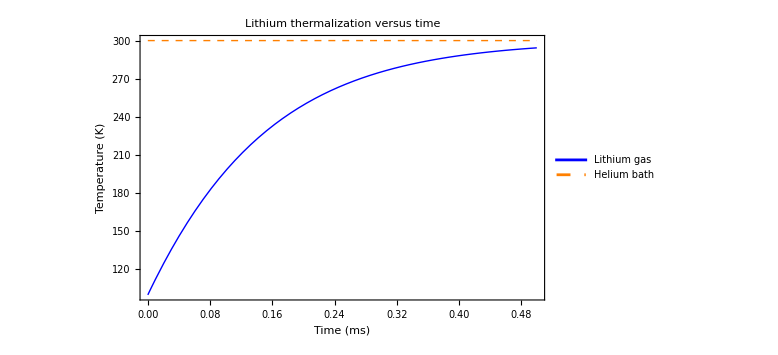
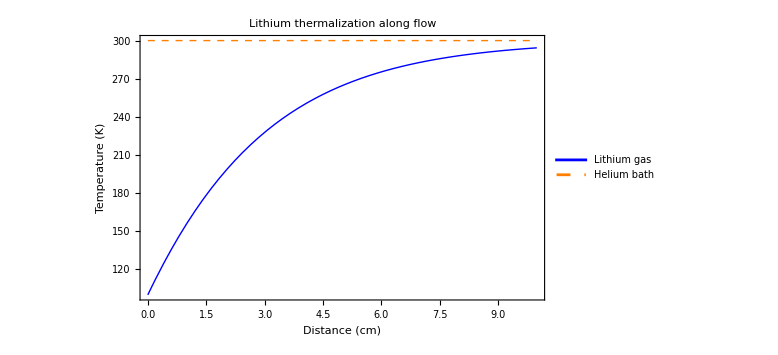
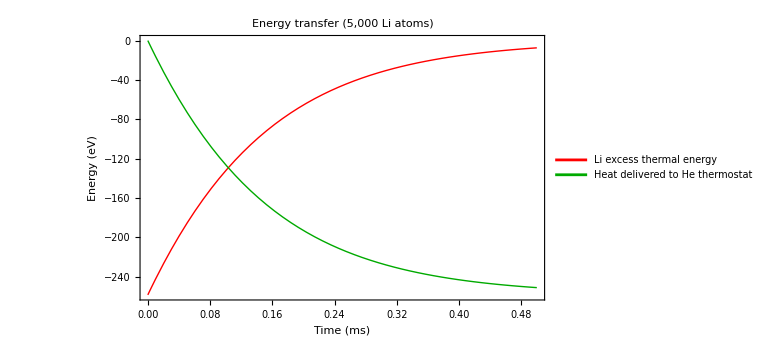
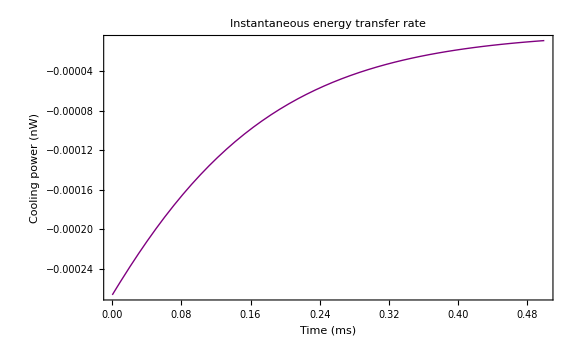
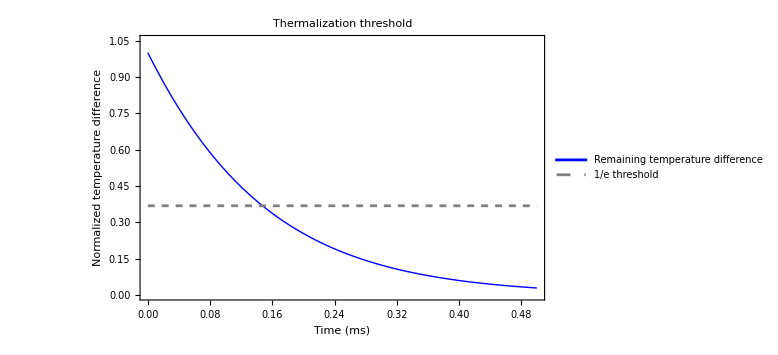

MODEL LIMITATIONS

This is a mean-temperature kinetic model, not a 5,000-particle trajectory simulation. The Li-He cross section is illustrative and must be replaced with a measured/calculated temperature-dependent transport cross section for quantitative predictions. The collision-rate approximation includes drift speed, but the energy-relaxation equation does not model directed-flow energy conversion, spatial diffusion, Li-Li collision kinetics, wall collisions, or non-Maxwellian velocity distributions. A constant He temperature and density are assumed throughout the cooling region.

```mathematica
(* ::Title:: *)
(* Flowing Lithium Gas Thermalization in a Helium Buffer Gas *)
(* ::Text:: *)
(* Edit ONLY the USER INPUTS section, then evaluate the whole file. *)
(* This is a spatially uniform, mean-temperature kinetic model, not molecular dynamics. *)

ClearAll["Global`*"];

(* ================================================================ *)
(* USER INPUTS -- CHANGE THESE VALUES *)
(* ================================================================ *)
inputs = <|
  "LithiumAtomCount" -> 10000,          (* number of Li atoms represented *)
  "LithiumIsotopeMassAMU" -> 7.,        (* 6 or 7 for common Li isotopes *)
  "HeliumMassAMU" -> 4.,
  "InitialLithiumTemperatureK" -> 100.,
  "HeliumTemperatureK" -> 300.,
  "HeliumNumberDensityM3" -> 1.*10^20, (* atoms/m^3; editable *)
  "LiHeCrossSectionM2" -> 1.*10^-19,   (* illustrative effective momentum-transfer cross section *)
  "CrossSectionTemperatureExponent" -> 0., (* sigma(T)=sigma0 (Tref/Trel)^exponent *)
  "CrossSectionReferenceTemperatureK" -> 300.,
  "EnergyAccommodationMultiplier" -> 1., (* 0..1; phenomenological adjustment *)
  "LithiumFlowSpeedMPerS" -> 200.,     (* Li axial velocity relative to apparatus *)
  "HeliumFlowSpeedMPerS" -> 0.,        (* axial He drift; affects relative collision speed *)
  "CoolingRegionLengthM" -> 0.10,     (* length of helium region *)
  "TimePlotMaximumMS" -> Automatic,   (* Automatic = transit time *)
  "PlotPoints" -> 120
|>;

(* ================================================================ *)
(* CONSTANTS AND VALIDATION *)
(* ================================================================ *)
kB = 1.380649*10^-23; (* J/K *)
amu = 1.66053906660*10^-27; (* kg *)
eV = 1.602176634*10^-19; (* J/eV *)

nLi = inputs["LithiumAtomCount"];
mLi = inputs["LithiumIsotopeMassAMU"] amu;
mHe = inputs["HeliumMassAMU"] amu;
tInitial = inputs["InitialLithiumTemperatureK"];
tBath = inputs["HeliumTemperatureK"];
nHe = inputs["HeliumNumberDensityM3"];
sigma0 = inputs["LiHeCrossSectionM2"];
alpha = inputs["EnergyAccommodationMultiplier"];
uLi = inputs["LithiumFlowSpeedMPerS"];
uHe = inputs["HeliumFlowSpeedMPerS"];
length = inputs["CoolingRegionLengthM"];
exponent = inputs["CrossSectionTemperatureExponent"];
tRef = inputs["CrossSectionReferenceTemperatureK"];

If[!And @@ {
   IntegerQ[nLi], nLi > 0, mLi > 0, mHe > 0,
   tInitial > 0, tBath > 0, nHe >= 0, sigma0 > 0,
   0 <= alpha <= 1, uLi > 0, length > 0, tRef > 0,
   NumericQ[exponent]
   },
  Print["ERROR: Check USER INPUTS (positive masses, temperatures, length, flow speed; 0<=accommodation<=1)."];
  Abort[];
];

residenceTime = length/uLi;
tEnd = If[inputs["TimePlotMaximumMS"] === Automatic,
  residenceTime, Min[residenceTime, inputs["TimePlotMaximumMS"]*10^-3]];
If[!NumericQ[tEnd] || tEnd <= 0, Print["ERROR: Invalid plot duration."]; Abort[]];

(* ================================================================ *)
(* COLLISION MODEL *)
(* ================================================================ *)
(* Relative thermal velocity for Maxwellian Li and He populations.
   Axial drift is included approximately in quadrature. *)
relativeSpeed[temp_?NumericQ] := Sqrt[
   (8. kB/Pi) (temp/mLi + tBath/mHe) + (uLi - uHe)^2
];

(* Illustrative temperature-dependent effective cross section. *)
relativeTemperature[temp_?NumericQ] := (mHe temp + mLi tBath)/(mLi + mHe);
effectiveSigma[temp_?NumericQ] := sigma0 (tRef/relativeTemperature[temp])^exponent;
collisionRate[temp_?NumericQ] := nHe effectiveSigma[temp] relativeSpeed[temp];

(* Isotropic, elastic binary-collision approximation for fractional
   relaxation of Li excess thermal energy per collision.
   This approximation does not fully describe drifting/non-Maxwellian flows. *)
xi = 2. mLi mHe/(mLi + mHe)^2;
relaxationRate[temp_?NumericQ] := alpha xi collisionRate[temp];

(* ================================================================ *)
(* SOLVE LITHIUM TEMPERATURE *)
(* ================================================================ *)
(* Treat Li atoms as a Maxwellian population with instantaneous mean T.
   Bath temperature is externally held constant. *)
sol = NDSolveValue[
   {temp'[time] == -relaxationRate[temp[time]] (temp[time] - tBath),
    temp[0] == tInitial},
   temp, {time, 0, tEnd},
   Method -> {"StiffnessSwitching"}, MaxSteps -> Infinity
];

liTemperature[time_?NumericQ] := sol[Clip[time, {0., tEnd}]];
liTemperatureAtPosition[z_?NumericQ] := liTemperature[z/uLi];

(* Monatomic ideal-gas thermal energy for the specified ensemble. *)
liExcessEnergy[time_?NumericQ] := 1.5 nLi kB (liTemperature[time] - tBath);
heHeatGained[time_?NumericQ] := 1.5 nLi kB (tInitial - liTemperature[time]);
coolingPower[time_?NumericQ] := 1.5 nLi kB relaxationRate[liTemperature[time]] (liTemperature[time] - tBath);
normalizedDifference[time_?NumericQ] := (liTemperature[time] - tBath)/(tInitial - tBath);

(* ================================================================ *)
(* THRESHOLD TIMES: SAFE BRACKETING BISECTION, NO FindRoot *)
(* ================================================================ *)
thresholdTime[fraction_?NumericQ] := Module[
  {target, lo = 0., hi = tEnd, mid, i},
  If[tInitial <= tBath || fraction <= 0 || fraction >= 1, Return[Missing["NotApplicable"]]];
  target = tBath + fraction (tInitial - tBath);
  If[liTemperature[tEnd] > target, Return[Missing["NotReachedBeforeExit"]]];
  Do[
    mid = (lo + hi)/2.;
    If[liTemperature[mid] > target, lo = mid, hi = mid],
    {i, 65}
  ];
  (lo + hi)/2.
];

tau1e = thresholdTime[Exp[-1.]];
t95 = thresholdTime[0.05];
t99 = thresholdTime[0.01];
formatTime[x_] := If[MissingQ[x], "Not reached before exit", NumberForm[10^3 x, {10, 5}]];

(* ================================================================ *)
(* RESULTS *)
(* ================================================================ *)
Print[Style["Flowing Li gas thermalization in a thermostatted He bath", 17, Bold]];
summary = Grid[{
  {"Li atoms represented", nLi},
  {"Initial Li temperature (K)", tInitial},
  {"He bath temperature (K)", tBath},
  {"He density (m^-3)", ScientificForm[nHe]},
  {"Effective Li-He cross section (m^2)", ScientificForm[sigma0]},
  {"Li axial speed (m/s)", uLi},
  {"He axial speed (m/s)", uHe},
  {"Cooling region length (m)", length},
  {"Residence time (ms)", 1000 residenceTime},
  {"Initial collision rate per Li atom (s^-1)", ScientificForm[collisionRate[tInitial]]},
  {"Fractional relaxation factor per collision", xi alpha},
  {"Li temperature at plotted exit (K)", liTemperature[tEnd]},
  {"1/e relaxation time (ms)", formatTime[tau1e]},
  {"95% relaxation time (ms)", formatTime[t95]},
  {"99% relaxation time (ms)", formatTime[t99]},
  {"Heat transferred by plotted exit (eV)", heHeatGained[tEnd]/eV},
  {"Energy balance error (J)", liExcessEnergy[tEnd] + heHeatGained[tEnd] - liExcessEnergy[0.]}
  }, Frame -> All, Alignment -> Left, ItemSize -> All];
Print[summary];

(* ================================================================ *)
(* PLOTS -- OPTIONS EXPLICIT TO AVOID Plot::nonopt *)
(* ================================================================ *)
plotEndMS = 1000 tEnd;
plotEndCM = 100 length (tEnd/residenceTime);

pTemperatureTime = Plot[
  Evaluate[{sol[ms/1000.], tBath}], {ms, 0, plotEndMS},
  Frame -> True, Axes -> False, PlotRange -> All,
  PlotStyle -> {Directive[Blue, Thick], Directive[Orange, Dashed, Thick]},
  PlotLegends -> {"Lithium gas", "Helium bath"},
  FrameLabel -> {"Time (ms)", "Temperature (K)"},
  PlotLabel -> "Lithium thermalization versus time", ImageSize -> Large
];

pTemperatureDistance = Plot[
  Evaluate[{sol[(cm/100.)/uLi], tBath}], {cm, 0, plotEndCM},
  Frame -> True, Axes -> False, PlotRange -> All,
  PlotStyle -> {Directive[Blue, Thick], Directive[Orange, Dashed, Thick]},
  PlotLegends -> {"Lithium gas", "Helium bath"},
  FrameLabel -> {"Distance (cm)", "Temperature (K)"},
  PlotLabel -> "Lithium thermalization along flow", ImageSize -> Large
];

pEnergy = Plot[
  Evaluate[{liExcessEnergy[ms/1000.]/eV, heHeatGained[ms/1000.]/eV}],
  {ms, 0, plotEndMS},
  Frame -> True, Axes -> False, PlotRange -> All,
  PlotStyle -> {Directive[Red, Thick], Directive[Darker[Green], Thick]},
  PlotLegends -> {"Li excess thermal energy", "Heat delivered to He thermostat"},
  FrameLabel -> {"Time (ms)", "Energy (eV)"},
  PlotLabel -> "Energy transfer (5,000 Li atoms)", ImageSize -> Large
];

pPower = Plot[
  Evaluate[10^9 coolingPower[ms/1000.]], {ms, 0, plotEndMS},
  Frame -> True, Axes -> False, PlotRange -> All,
  PlotStyle -> Directive[Purple, Thick],
  FrameLabel -> {"Time (ms)", "Cooling power (nW)"},
  PlotLabel -> "Instantaneous energy transfer rate", ImageSize -> Large
];

pNormalized = Plot[
  Evaluate[{normalizedDifference[ms/1000.], Exp[-1.]}],
  {ms, 0, plotEndMS},
  Frame -> True, Axes -> False, PlotRange -> {0, 1.05},
  PlotStyle -> {Directive[Blue, Thick], Directive[Gray, Dashed]},
  PlotLegends -> {"Remaining temperature difference", "1/e threshold"},
  FrameLabel -> {"Time (ms)", "Normalized temperature difference"},
  PlotLabel -> "Thermalization threshold", ImageSize -> Large
];

Print[Column[{pTemperatureTime, pTemperatureDistance, pEnergy, pPower, pNormalized}, Spacings -> 2]];

Print[Style["MODEL LIMITATIONS", Bold, 13]];
Print["This is a mean-temperature kinetic model, not a 5,000-particle trajectory simulation. ",
 "The Li-He cross section is illustrative and must be replaced with a measured/calculated ",
 "temperature-dependent transport cross section for quantitative predictions. ",
 "The collision-rate approximation includes drift speed, but the energy-relaxation ",
 "equation does not model directed-flow energy conversion, spatial diffusion, ",
 "Li-Li collision kinetics, wall collisions, or non-Maxwellian velocity distributions. ",
 "A constant He temperature and density are assumed throughout the cooling region."];
```